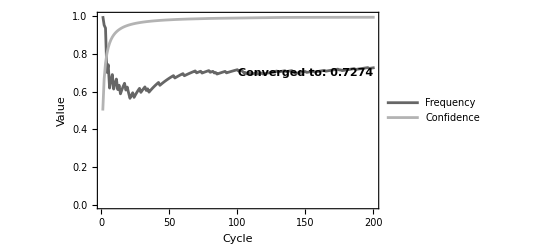

```mathematica
(* Define initial parameters *)
	k=1; (* Evidential horizon personality factor *)
	maxCycles=200;
	userProbability=0.8; (* User-defined probability for events at S and P *)
	negativeEvidence={0.0,0.5}; (* Default negative evidence truth value *)
	
	(* Initialize truth values *)
	initialTruthValue={1.0,0.5};
	truthValues={initialTruthValue};
	
	(* Function to compute weights from truth values *)
	f2w[f_,c_,k_]:=(k*f*c)/(1-c)
	c2w[c_,k_]:=(k*c)/(1-c)

(* Define the ReverseRevision function *)
reverseRevision[revised_,truth2_,k_]:=Module[
  {revisedF,revisedC,f2,c2,wTotal,wPlusTotal,w2,wPlus2,w1,wPlus1,originalFrequency,originalConfidence},
  
  (* Deconstruct the inputs *)
  {revisedF,revisedC}=revised;
  {f2,c2}=truth2;
  
  (* Calculate total evidence and positive evidence added by the revision *)
  wTotal=c2w[revisedC,k];           (* Total evidence of the combined truth *)
  wPlusTotal=f2w[revisedF,revisedC,k];  (* Positive evidence of the combined truth *)
  w2=c2w[c2,k];                     (* Total evidence of truth2 *)
  wPlus2=f2w[f2,c2,k];             (* Positive evidence of truth2 *)
  
  (* Subtract evidence of truth2 from the combined evidence *)
  w1=wTotal-w2;                    (* Remaining total evidence corresponds to truth1 *)
  wPlus1=wPlusTotal-wPlus2;        (* Remaining positive evidence corresponds to truth1 *)
  
  (* Reverse the frequency and confidence of truth1 *)
  originalFrequency=wPlus1 / w1;
  originalConfidence=w1 / (w1 +k);
  
  (* Return the original truth1 values rounded to 4 decimal places *)
  {Round[originalFrequency,0.0001],Round[originalConfidence,0.0001]}
]
	
	(* Function to revise link strength *)
	reviseTruthValues[truth1_,truth2_,k_]:=Module[
	  {f1,c1,f2,c2,wPlus,w,revisedF,revisedC},
	  {f1,c1}=truth1;
	  {f2,c2}=truth2;
	  wPlus=f2w[f1,c1,k]+f2w[f2,c2,k];
	  w=c2w[c1,k]+c2w[c2,k];
	  revisedF=wPlus/w;
	  revisedC=w/(w+k);
	  {revisedF,revisedC}
	];
	
	(* Simulate cycles *)
	For[cycle=1,cycle<=maxCycles,cycle++,
	  (* Simulate event occurrence at S *)
	  newTruthValue=reviseTruthValues[truthValues[[-1]],negativeEvidence,k];
	  
	  (* Check for joint event occurrence of S and P *)
	  If[RandomReal[]<userProbability,
	    (* Remove negative evidence and add positive evidence if joint event occurs *)
		{newTruthValue=reverseRevision[newTruthValue,negativeEvidence,k],	   
	    newTruthValue=reviseTruthValues[newTruthValue,{1.0*Exp[-0.01*10],0.5},k]},
		newTruthValue
	  ];
	  
	  AppendTo[truthValues,newTruthValue];
	]	
	(* Plot the convergence of truth values and expectation *)
	ListLinePlot[
	  {truthValues[[All,1]],truthValues[[All,2]]},
	  PlotRange->{{1,maxCycles},{0,1}},
	  Frame->True,
	  FrameLabel->{"Cycle","Value"},
	  PlotStyle->{GrayLevel[0.4],GrayLevel[0.7]},
            PlotLegends->Placed[{"Frequency","Confidence"},{0.8,0.2}],
Epilog->{
    Text[
      Style["Converged to: " <>ToString[
        NumberForm[truthValues[[-1,1]],{4,4}]],
        Bold,
        Black
      ],
      {maxCycles,truthValues[[-1,1]]},
      {1.1,2.5}
    ]
  }
	]
```